#### Antiimagen de la circunferencia unidad

a y b son números complejos: a=a1+b1*I; b=b1+b2*I;

```mathematica
moeb[z_]=(z-a)/(z-b); invmoeb[z_]=(b*z-a)/(z-1);
```

```mathematica
invmoeb[Exp[I*x]]//ComplexExpand//Simplify
```

(-a+b Cos[x]+ⅈ b Sin[x])/(-1+Cos[x]+ⅈ Sin[x])

Lo desarrollo un poco (igualo esto lo puedes hacer de una manera más eficiente)

```mathematica
(-a+b Cos[x]+ⅈ b Sin[x])*(-1+Cos[x]-ⅈ Sin[x])//ComplexExpand//FullSimplify
```

a+b-(a+b) Cos[x]+ⅈ (a-b) Sin[x]

```mathematica
(-1+Cos[x]+ⅈ Sin[x])*(-1+Cos[x]-ⅈ Sin[x])//ComplexExpand//FullSimplify
```

2-2 Cos[x]

Parte real :

```mathematica
(a+b-(a+b) Cos[x])/(2-2 Cos[x])//Simplify
```

(a+b)/2

Parte imaginaria :

```mathematica
(a-b) Sin[x]/(2-2 Cos[x])//Simplify
```

1/2 (a-b) Cot[x/2]

Desarrollo los complejos:

```mathematica
(a+b)/2+I(1/2 (a-b) Cot[x/2])/.a->a1+I*a2/.b->b1+I*b2//ComplexExpand//FullSimplify
```

1/2 (a1+ⅈ a2+b1+ⅈ b2+(ⅈ a1-a2-ⅈ b1+b2) Cot[x/2])

En paramétricas quedaría:
x=1/2 (a1+b1+(-a2+b2) Cot[t/2])
y=1/2 ( a2+ b2+(a1- b1) Cot[t/2])
que es la expresión en paramétricas de la bisectriz

Un ejemplo

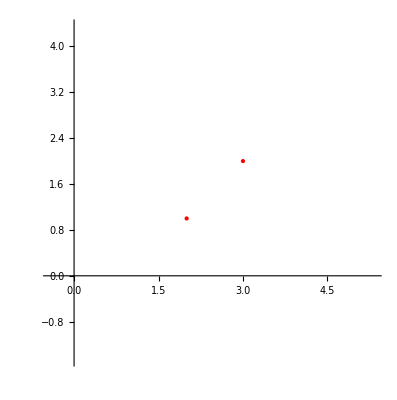

```mathematica
a1=2;a2=1;b1=3;b2=2;Show[ParametricPlot[{1/2 (a1+b1+(-a2+b2) Cot[t/2]),1/2 ( a2+ b2+(a1- b1) Cot[t/2])},{t,0,2Pi}],Graphics[{Red,Point[{a1,a2}]}],Graphics[{Red,Point[{b1,b2}]}]]
```